## Setup

```mathematica
Get["FunKit`"]
```

Loading external dependencies...

TensorBases loaded

MaTeX loaded

Loading modules...

...FEDeriK loaded

...AnSEL loaded

...DiANE loaded

...DiRK loaded

...TRACY loaded

...COEN loaded

...SeDecA loaded

Welcome to  █▀ ▐▄█ █▚▌ ▐◀ █ ▀█▀
Author: Franz Richard Sattler
Version: 1.0
Year: 2025
For more information, call FInfo[].

```mathematica
fields= <|
"cField"-> {A[p,{v, c}]},
"Grassmann"->{{cb[p,{c}],c[p,{c}]}}
|>;
truncation=<|
GammaN->{{A,A},{A,A,A},{A,A,A,A},{A,cb,c},{cb,c}},
Propagator->{{A,A},{cb,c}},Rdot->{{A,A},{cb,c}},
S->{{A,A},{A,A,A},{A,A,A,A},{cb,c},{cb,c,A}},
Field->{{}}
|>;
bases=<|
GammaN->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
S->{{A,A}->{"AA",1},{A,A,A}->"AAAClass",{A,A,A,A}->"AAAAClass",{A,cb,c}->{"Acbc",1},{cb,c}->"cbc"},
Propagator->{{A,A}->"AA",{cb,c}->"cbc"},
Rdot->{{A,A}->{"AA",1},{cb,c}->"cbc"}
|>;
diagramStyling=<|
"Styles"->{A->{Orange},c->{Black,Dashed}}
|>;
Setup=<|
"FieldSpace"->fields,
"Truncation"->truncation,
"FeynmanRules"->bases,
"DiagramStyling"->diagramStyling
|>;

FSetTexStyles[cb->"\\bar{c}"];
FSetGlobalSetup[Setup];
dressingRules=ReplaceRepeated[#,{
dressing[GammaN,{A,A},2,{a_,b_}]:>1,
dressing[GammaN,{c,cb},1,{p1_,p2_}]:>Zc[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{A,A},1,{p1_,p2_}]:>ZA[√sp[p2,p2]]sp[p2,p2],
dressing[GammaN,{c,cb,A},1,{p1_,p2_,p3_}]:>ZccbA[p1,p2], 
dressing[GammaN,{A,A,A},1,{p1_,p2_,p3_}]:>ZA3[p1,p2], 
dressing[GammaN,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>ZA4[p1,p2,p3] ,

dressing[S,{c,cb,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A},1,{p1_,p2_,p3_}]:>gS, 
dressing[S,{A,A,A,A},1,{p1_,p2_,p3_,p4_}]:>gS^2,

dressing[S,{c,cb},1,{p1_,p2_}]->sp[p2,p2],
dressing[S,{A,A},1,{p1_,p2_}]->sp[p2,p2],

ZccbA[p1_,p2_]:>ZccbA[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA3[p1_,p2_]:>ZA3[√(1/3(sp[p1,p1]+sp[p2,p2]+sp[-p1-p2,-p1-p2]))],
ZA4[p1_,p2_,p3_]:>ZA4[√(1/4(sp[p1,p1]+sp[p2,p2]+sp[p3,p3]+sp[-p1-p2-p3,-p1-p2-p3]))],

nZA->6,
evP:>(k^nZA+1)^(1/nZA),
devP:>k^(-1+nZA) (1+k^nZA)^(-1+1/nZA),
dressing[Rdot,{A,A},1,{p1_,p2_}]:>ZA[evP]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZA[evP]+k*devP*((ZA[1.02evP]-ZA[evP])/(0.02*evP))),
dressing[Rdot,{c,cb},1,{p1_,p2_}]:>Zc[k]RBdot[k^2,sp[p2,p2]]+RB[k^2,sp[p2,p2]](dtZc[k]+k((Zc[1.02*k]-Zc[k])/(0.02*k)))
}]&;

SetSymmetricDressing[GammaN,{A,A}]
PropParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p1,p1]->p^2,sp[l2,l2]->l2^2,sp[l1,l1]->l1^2,sp[l1,p1]->l1 p cos[p,l1],sp[l2,p1]->l2 p cos[p,l2],sp[l1,l2]->l1 l2 cos[l1,l2],√(a_^2):>a,(a_^2)^(n_/2):>a^n}//FORMSimplify;
SPParam[expr_]:=UseLorentzLinearity[expr]//.{sp[p,p]->p^2,sp[l1,l1]->l1^2,sp[l1,l2]->l1 l2 cos[l1,l2],√(a_^2):>a,(a_^2)^(n_/2):>a^n,(a_^2)^(n_/2):>a^n,Power[Power[l1_,2],Rational[n_,2]]:>l1^n}//FORMSimplify;
SetNc[3]
$Assumptions=k>0&&p>0&&l1>0&&-1<cos1<1-1<cos2<1&&-1<cos3<1;
```

## DSE

## 2-Point

```mathematica
symmetryP2={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2}]],{i1,i2}};
```


-Graphics-+-Graphics-/2--Graphics-/2--Graphics-/6--Graphics-+-Graphics-/2

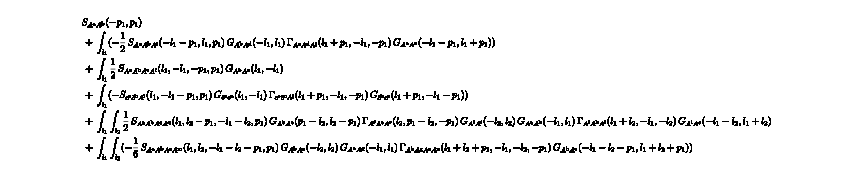

auto DSEAA1Loop(const auto &l1, const auto &p, const auto &cos, const auto &gS, const auto &ZA, const auto &Zc,
                const auto &ZA3, const auto &ZccbA)
{
  const auto _repl1 = ZA(l1);
  const auto _repl2 = cos(p, l1);
  const auto _repl3 = ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p, l1)));
  return (2. * gS + gS * powr<-2>(l1) * (7. + (-1. + _repl1 * powr<2>(l1)) * powr<2>(_repl2)) / (_repl1) +
          -0.5 * powr<-1>(_repl3) * powr<-2>(l1) * powr<-2>(powr<2>(l1) + 2. * _repl2 * l1 * p + powr<2>(p)) *
              ZA3(0.816496580927726 * sqrt(powr<2>(l1) + _repl2 * l1 * p + powr<2>(p))) *
              (4. * (-1. + _repl1 * powr<2>(l1)) * powr<4>(_repl2) * powr<2>(l1) * powr<2>(p) +
               (2. * powr<6>(l1) + 3. * powr<4>(l1) * powr<2>(p) +
                _repl3 * (powr<2>(l1) + powr<2>(p)) * powr<2>(l1) * powr<4>(p)) *
                   _repl1 +
               (6. * powr<4>(l1) + 16. * powr<2>(l1) * powr<2>(p) + 6. * powr<4>(p) +
                _repl3 * (powr<2>(l1) + powr<2>(p)) * powr<2>(powr<2>(l1) + -1. * powr<2>(p))) *
                   2. +
               2. *
                   (2. * _repl3 * powr<2>(powr<2>(l1) + -1. * powr<2>(p)) + (powr<2>(l1) + powr<2>(p)) * 12. +
                    _repl1 * (7. * powr<2>(l1) + 6. * powr<2>(p) + _repl3 * powr<4>(p)) * powr<2>(l1)) *
                   _repl2 * l1 * p +
               (_repl3 * (powr<2>(l1) + powr<2>(p)) * powr<2>(powr<2>(l1) + -1. * powr<2>(p)) +
                (3. * powr<4>(l1) + 7. * powr<2>(l1) * powr<2>(p) + 3. * powr<4>(p)) * -4. +
                _repl1 *
                    (powr<4>(l1) + 32. * powr<2>(l1) * powr<2>(p) + 12. * powr<4>(p) +
                     -1. * (powr<2>(l1) + powr<2>(p)) * _repl3 * powr<4>(p)) *
                    powr<2>(l1)) *
                   powr<2>(_repl2) +
               2. *
                   (_repl3 * powr<2>(powr<2>(l1) + -1. * powr<2>(p)) + (powr<2>(l1) + powr<2>(p)) * -12. +
                    _repl1 * (-1. * _repl3 * powr<4>(p) + (powr<2>(l1) + 6. * powr<2>(p)) * 2.) * powr<2>(l1)) *
                   powr<3>(_repl2) * l1 * p) /
              (_repl1) +
          powr<-1>(Zc(l1)) * powr<-1>(Zc(sqrt(powr<2>(l1) + 2. * _repl2 * l1 * p + powr<2>(p)))) *
              ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + _repl2 * l1 * p + powr<2>(p))) * (-1. + powr<2>(_repl2)) /
              (powr<2>(l1) + 2. * _repl2 * l1 * p + powr<2>(p))) *
         gS;
}

```mathematica
DSEAA=FTakeDerivatives[MakeDSE[Setup,A[i1]],{A[i2]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP2]&//FPlot//FRoute//FPrint;
DSEAAResult=Map[
(FormTrace[
F[TBGetProjector["AA",1,{i1,i2}/.#["ExternalIndices"]],#["Expression"]/.MakeDiagrammaticRules[]]
]//dressingRules//FORMSimplify//PropParam)&,
DSEAA]
MakeCppFunction[DSEAAResult["1-Loop"],"Name"->"DSEAA1Loop","Parameters"->{"l1","p","cos","gS","ZA","Zc","ZA3","ZccbA"}]
```

```mathematica
DSEcbc=FTakeDerivatives[MakeDSE[Setup,c[i1]],{cb[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
DSEcbcResult=Map[
(FormTrace[
F[TBGetProjector["cbc",1,{i1,i2}/.#["ExternalIndices"]],#["Expression"]/.MakeDiagrammaticRules[]]
]//dressingRules//FORMSimplify//PropParam)&,
DSEcbc]
MakeCppFunction[DSEcbcResult["1-Loop"],"Name"->"DSEcbc1Loop","Parameters"->{"l1","p","cos","gS","ZA","Zc","ZA3","ZccbA"}]
```

-Graphics-+-Graphics-

-Graphics-

<|0-Loop→p^2,1-Loop→(3 gS p^2 (-1+cos[p,l1]^2) ZccbA[0.816497 √(l1^2+p^2+l1 p cos[p,l1])])/(l1^2 (l1^2+p^2+2 l1 p cos[p,l1]) ZA[l1] Zc[√(l1^2+p^2+2 l1 p cos[p,l1])])|>

auto DSEcbc1Loop(const auto &l1, const auto &p, const auto &cos, const auto &gS, const auto &ZA, const auto &Zc,
                 const auto &ZA3, const auto &ZccbA)
{
  const auto _repl1 = cos(p, l1);
  return 3. * gS * powr<-2>(l1) * powr<2>(p) * powr<-1>(ZA(l1)) *
         powr<-1>(Zc(sqrt(powr<2>(l1) + 2. * _repl1 * l1 * p + powr<2>(p)))) *
         ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + _repl1 * l1 * p + powr<2>(p))) * (-1. + powr<2>(_repl1)) /
         (powr<2>(l1) + 2. * _repl1 * l1 * p + powr<2>(p));
}

## 3Point

```mathematica
symmetryP3={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3}]],{i1,i2,i3}};
SP3FormRule=MakeSPFormRule[{l1},p,{p1,p2,p3}];
```

```mathematica
DSEAcbc=FTakeDerivatives[MakeDSE[Setup,c[i1]],{A[i3],cb[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
DSEAcbcResult=Map[
(FormTrace[
F[TBGetProjector["Acbc",1,{i3,i2,i1}/.#["ExternalIndices"]],#["Expression"]/.MakeDiagrammaticRules[]]
,SP3FormRule,SP3FormRule]//dressingRules//(FORMSimplify[#,SP3FormRule,SP3FormRule]&)//SPParam)&,
DSEAcbc]
MakeCppFunction[DSEAcbcResult["1-Loop"],"Name"->"DSEAcbc1Loop","Parameters"->{"l1","p","cos","gS","ZA","Zc","ZA3","ZccbA"}]
```

-Graphics---Graphics-+-Graphics-

-Graphics-

<|0-Loop→gS,1-Loop→1/(l1^2 ZA[l1])gS ((p (3 p+2 l1 cos[p1,l1]-2 l1 cos[p2,l1]) (1+2 cos[p1,l1] cos[p2,l1]) ZccbA[0.816497 √(l1^2+p^2-l1 p cos[p2,l1])] ZccbA[√((2 l1^2)/3+p^2+2/3 l1 p cos[p1,l1]-2/3 l1 p cos[p2,l1])])/(4 (l1^2+p^2+2 l1 p cos[p1,l1]) (l1^2+p^2-2 l1 p cos[p2,l1]) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2-2 l1 p cos[p2,l1])])+((3 p^4 (-1/2+cos[p1,l1] cos[p2,l1]+cos[p2,l1]^2)+l1 (p^3 (7 cos[p2,l1] (-1/2+cos[p2,l1]^2)+cos[p1,l1] (-5/2+5 cos[p1,l1] cos[p2,l1]+12 cos[p2,l1]^2))+l1 p (l1 cos[p2,l1]+3 p (-1+2 cos[p2,l1]^2)+l1 cos[p1,l1] (-1-2 cos[p1,l1] cos[p2,l1]+2 cos[p2,l1]^2)+p cos[p1,l1] (cos[p1,l1]+5 cos[p2,l1]-2 cos[p1,l1]^2 cos[p2,l1]+2 cos[p2,l1]^3)))) ZA3[0.816497 √(l1^2+p^2+l1 p cos[p1,l1]+l1 p cos[p2,l1])] ZccbA[0.816497 √(l1^2+p^2+l1 p cos[p2,l1])])/((l1^2+p^2+2 l1 p cos[p2,l1]) (l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])^2 ZA[√(l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])] Zc[√(l1^2+p^2+2 l1 p cos[p2,l1])]))|>

auto DSEAcbc1Loop(const auto &l1, const auto &p, const auto &cos, const auto &gS, const auto &ZA, const auto &Zc,
                  const auto &ZA3, const auto &ZccbA)
{
  const auto _repl1 = cos(p1, l1);
  const auto _repl2 = cos(p2, l1);
  return gS * powr<-2>(l1) *
         (0.25 * p * powr<-1>(Zc(sqrt(powr<2>(l1) + 2. * _repl1 * l1 * p + powr<2>(p)))) *
              powr<-1>(Zc(sqrt(powr<2>(l1) + -2. * _repl2 * l1 * p + powr<2>(p)))) *
              ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + -1. * _repl2 * l1 * p + powr<2>(p))) *
              ZccbA(sqrt(0.6666666666666666 * powr<2>(l1) + 0.6666666666666666 * _repl1 * l1 * p +
                         -0.6666666666666666 * _repl2 * l1 * p + powr<2>(p))) *
              (2. * _repl1 * l1 + -2. * _repl2 * l1 + 3. * p) / (powr<2>(l1) + -2. * _repl2 * l1 * p + powr<2>(p)) *
              (1. + 2. * _repl1 * _repl2) / (powr<2>(l1) + 2. * _repl1 * l1 * p + powr<2>(p)) +
          powr<-2>(powr<2>(l1) + 2. * _repl1 * l1 * p + 2. * _repl2 * l1 * p + powr<2>(p)) *
              powr<-1>(ZA(sqrt(powr<2>(l1) + 2. * _repl1 * l1 * p + 2. * _repl2 * l1 * p + powr<2>(p)))) *
              ZA3(0.816496580927726 * sqrt(powr<2>(l1) + _repl1 * l1 * p + _repl2 * l1 * p + powr<2>(p))) *
              powr<-1>(Zc(sqrt(powr<2>(l1) + 2. * _repl2 * l1 * p + powr<2>(p)))) *
              ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + _repl2 * l1 * p + powr<2>(p))) *
              (3. * (-0.5 + _repl1 * _repl2 + powr<2>(_repl2)) * powr<4>(p) +
               ((7. * (-0.5 + powr<2>(_repl2)) * _repl2 +
                 (-2.5 + 5. * _repl1 * _repl2 + 12. * powr<2>(_repl2)) * _repl1) *
                    powr<3>(p) +
                l1 *
                    (_repl2 * l1 + _repl1 * (-1. + -2. * _repl1 * _repl2 + 2. * powr<2>(_repl2)) * l1 +
                     3. * (-1. + 2. * powr<2>(_repl2)) * p +
                     _repl1 * (_repl1 + 5. * _repl2 + -2. * powr<2>(_repl1) * _repl2 + 2. * powr<3>(_repl2)) * p) *
                    p) *
                   l1) /
              (powr<2>(l1) + 2. * _repl2 * l1 * p + powr<2>(p))) /
         (ZA(l1));
}

-Graphics---Graphics-/2--Graphics-+-Graphics-+-Graphics-/2+-Graphics--2 -Graphics---Graphics---Graphics-

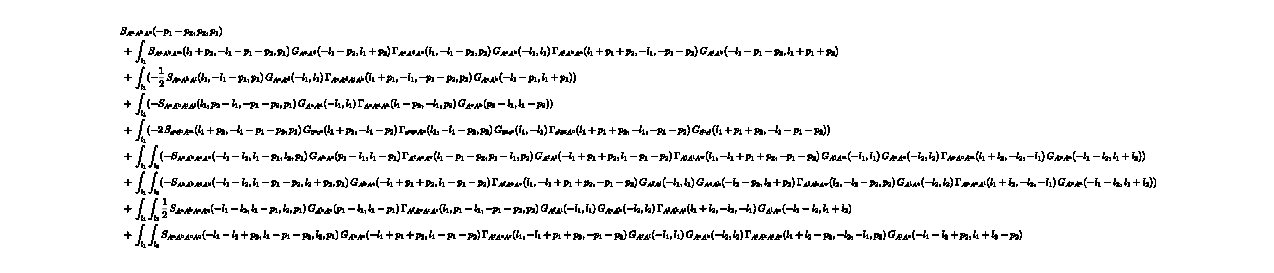

```mathematica
DSEA3=FTakeDerivatives[MakeDSE[Setup,A[i1]],{A[i3],A[i2]},"Symmetries"->symmetryP3]//FTruncate//FSimplify[#,"Symmetries"->symmetryP3]&//FPlot//FRoute//FPrint;
DSEA3Result=Map[
(FormTrace[
F[TBGetProjector["AAAClassTrans",1,{i3,i2,i1}/.#["ExternalIndices"]],#["Expression"]/.MakeDiagrammaticRules[]]
,SP3FormRule,SP3FormRule]//dressingRules//(FORMSimplify[#,SP3FormRule,SP3FormRule]&)//SPParam)&,
DSEA3]
```

## 4Point

```mathematica
symmetryP4={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4}]],{i1,i2,i3,i4}};
```

```mathematica
DSEA4=FTakeDerivatives[MakeDSE[Setup,A[i1]],{A[i4],A[i3],A[i2]},"Symmetries"->symmetryP4]//FTruncate//FSimplify[#,"Symmetries"->symmetryP4]&//FPlot//FRoute//FPrint;
```

24 -Graphics--36 -Graphics-+18 -Graphics-+72 -Graphics-+36 -Graphics--18 -Graphics--36 -Graphics--36 -Graphics--72 -Graphics--72 -Graphics--72 -Graphics--6 -Graphics-+72 -Graphics-+144 -Graphics-+24 -Graphics-

-Graphics-

## fRG

## 2-Point

```mathematica
symmetryP2={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2}]],{i1,i2}};
```


--Graphics-/2-2 -Graphics-+-Graphics-

-Graphics-

auto FlowAA(const auto &l1, const auto &p, const auto &cos, const auto &gS, const auto &ZA, const auto &Zc,
            const auto &ZA3, const auto &ZccbA)
{
  return -4. *
             (dtZA(pow(1. + powr<6>(k), 0.16666666666666666667)) * (1. + powr<6>(k)) * RB(powr<2>(k), powr<2>(l1)) +
              RBdot(powr<2>(k), powr<2>(l1)) * (1. + powr<6>(k)) * ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
              -50. *
                  (ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
                   -1. * ZA(1.02 * pow(1. + powr<6>(k), 0.16666666666666666667))) *
                  powr<6>(k) * RB(powr<2>(k), powr<2>(l1))) *
             powr<-4>(l1) * powr<-2>(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p, l1)) * powr<-2>(ZA(l1)) *
             powr<2>(ZA3(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p, l1)))) *
             (3. * powr<4>(l1) + 8. * powr<2>(l1) * powr<2>(p) + 3. * powr<4>(p) +
              6. * (powr<2>(l1) + powr<2>(p)) * l1 * p * cos(p, l1) + powr<2>(l1) * powr<2>(p) * powr<2>(cos(p, l1))) /
             (ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p, l1)))) * (-1. + powr<2>(cos(p, l1))) /
             (1. + powr<6>(k)) +
         powr<-4>(l1) *
             (-1. * RBdot(powr<2>(k), powr<2>(l1)) * ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
              (-1. * dtZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
               50. * powr<6>(k) *
                   (ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
                    -1. * ZA(1.02 * pow(1. + powr<6>(k), 0.16666666666666666667))) /
                   (1. + powr<6>(k))) *
                  RB(powr<2>(k), powr<2>(l1))) *
             (-1. * powr<2>(powr<2>(l1) + -1. * powr<2>(p)) *
                  powr<2>(ZA3(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p, l1)))) *
                  (2. + powr<2>(cos(p, l1))) / (powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p, l1)) +
              -1. * (-7. + powr<2>(cos(p, l1))) * ZA4(0.7071067811865475 * sqrt(powr<2>(l1) + powr<2>(p)))) *
             powr<-2>(ZA(l1)) +
         -2. * powr<-2>(l1) * powr<-2>(Zc(l1)) *
             powr<2>(ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + -1. * l1 * p * cos(p, l1)))) *
             (dtZc(k) * RB(powr<2>(k), powr<2>(l1)) + RBdot(powr<2>(k), powr<2>(l1)) * Zc(k) +
              -50. * (Zc(k) + -1. * Zc(1.02 * k)) * RB(powr<2>(k), powr<2>(l1))) /
             (Zc(sqrt(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p, l1)))) * (-1. + powr<2>(cos(p, l1))) /
             (powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p, l1))("1-Loop");
}

```mathematica
fRGAA=FTakeDerivatives[WetterichEquation,{A[i1],A[i2]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP2]&//FPlot//FRoute//FPrint;
traceExprAA=F[TBGetProjector["AA",1,{i1,i2}/.fRGAA["1-Loop"]["ExternalIndices"]],(fRGAA["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
FlowAA=FormTrace[traceExprAA]//dressingRules//FORMSimplify//PropParam;
MakeCppFunction[FlowAA["1-Loop"],"Name"->"FlowAA","Parameters"->{"l1","p","cos","gS","ZA","Zc","ZA3","ZccbA"}]
```

```mathematica
fRGcbc=FTakeDerivatives[WetterichEquation,{cb[i1],c[i2]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
traceExprcbc=F[TBGetProjector["cbc",1,{i1,i2}/.fRGcbc["1-Loop"]["ExternalIndices"]],(fRGcbc["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
Flowcbc=FormTrace[traceExprcbc]//dressingRules//FORMSimplify//PropParam
MakeCppFunction[Flowcbc["1-Loop"],"Name"->"Flowcbc","Parameters"->{"l1","p","cos","gS","ZA","Zc","ZA3","ZccbA"}]
```

--Graphics---Graphics-

-Graphics-

1/(l1^4 (l1^2+p^2+2 l1 p cos[p,l1])^2)3 p^2 (-(l1^2 (1-cos[p,l1]^2) (RBdot[k^2,l1^2] Zc[k]+RB[k^2,l1^2] (dtZc[k]+50 (-Zc[k]+Zc[(51 k)/50]))))/(ZA[√(l1^2+p^2+2 l1 p cos[p,l1])] Zc[l1]^2)-((l1^2+p^2+2 l1 p cos[p,l1]) (-1+cos[p,l1]^2) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])))/((1+k^6) ZA[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p,l1])])) ZccbA[0.816497 √(l1^2+p^2+l1 p cos[p,l1])]^2

auto Flowcbc(const auto &l1, const auto &p, const auto &cos, const auto &gS, const auto &ZA, const auto &Zc,
             const auto &ZA3, const auto &ZccbA)
{
  return 3. *
         (-1. *
              (RBdot(powr<2>(k), powr<2>(l1)) * Zc(k) +
               (dtZc(k) + (-1. * Zc(k) + Zc(1.02 * k)) * 50.) * RB(powr<2>(k), powr<2>(l1))) *
              powr<2>(l1) * powr<-2>(Zc(l1)) * (1. + -1. * powr<2>(cos(p, l1))) /
              (ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p, l1)))) +
          -1. *
              (dtZA(pow(1. + powr<6>(k), 0.16666666666666666667)) * (1. + powr<6>(k)) * RB(powr<2>(k), powr<2>(l1)) +
               RBdot(powr<2>(k), powr<2>(l1)) * (1. + powr<6>(k)) * ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
               -50. *
                   (ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
                    -1. * ZA(1.02 * pow(1. + powr<6>(k), 0.16666666666666666667))) *
                   powr<6>(k) * RB(powr<2>(k), powr<2>(l1))) *
              powr<-2>(ZA(l1)) * (-1. + powr<2>(cos(p, l1))) /
              (Zc(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p, l1)))) *
              (powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p, l1)) / (1. + powr<6>(k))) *
         powr<-4>(l1) * powr<2>(p) * powr<-2>(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p, l1)) *
         powr<2>(ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p, l1))))("1-Loop");
}

## 3Point

```mathematica
symmetryP3={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3}]],{i1,i2,i3}};
SP3FormRule=MakeSPFormRule[{l1},p,{p1,p2,p3}];
```

```mathematica
fRGAcbc=FTakeDerivatives[WetterichEquation,{A[i1],cb[i2],c[i3]}]//FTruncate//FSimplify//FPlot//FRoute//FPrint;
projectorAcbc=TBGetProjector["Acbc",1,{i1,i2,i3}/.fRGAcbc["1-Loop"]["ExternalIndices"]];
traceExprAcbc=F[projectorAcbc,(fRGAcbc["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];FlowAcbc=FormTrace[traceExprAcbc,SP3FormRule,SP3FormRule]//dressingRules//FORMSimplify[#,SP3FormRule,SP3FormRule]&//SPParam
MakeCppFunction[FlowAcbc["1-Loop"],"Name"->"FlowAcbc","Parameters"->{"l1","p","cos","gS","ZA","Zc","ZA3","ZccbA"}]
```

--Graphics---Graphics-+-Graphics-+-Graphics-+-Graphics---Graphics-

-Graphics-

(p (3 p-2 l1 cos[p1,l1]-4 l1 cos[p2,l1]) (-1+2 cos[p1,l1] cos[p2,l1]+2 cos[p2,l1]^2) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZccbA[√((2 l1^2)/3+p^2-2/3 l1 p cos[p1,l1]-4/3 l1 p cos[p2,l1])] ZccbA[0.816497 √(l1^2+p^2-l1 p cos[p2,l1])] ZccbA[0.816497 √(l1^2+p^2-l1 p cos[p1,l1]-l1 p cos[p2,l1])])/(4 (1+k^6) l1^4 (l1^2+p^2-2 l1 p cos[p2,l1]) (l1^2+p^2-2 l1 p cos[p1,l1]-2 l1 p cos[p2,l1]) ZA[l1]^2 Zc[√(l1^2+p^2-2 l1 p cos[p2,l1])] Zc[√(l1^2+p^2-2 l1 p cos[p1,l1]-2 l1 p cos[p2,l1])])+(p (cos[p1,l1]+2 cos[p2,l1]) (-l1+p cos[p2,l1]+2 l1 cos[p2,l1]^2+2 cos[p1,l1] (p+l1 cos[p2,l1])) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[0.816497 √(l1^2+p^2-l1 p cos[p1,l1])] ZccbA[√((2 l1^2)/3+p^2-2/3 l1 p cos[p1,l1]+2/3 l1 p cos[p2,l1])] ZccbA[0.816497 √(l1^2+p^2+l1 p cos[p2,l1])])/(2 l1^2 (l1^2+p^2-2 l1 p cos[p1,l1]) (l1^2+p^2+2 l1 p cos[p2,l1])^2 ZA[√(l1^2+p^2+2 l1 p cos[p2,l1])] Zc[l1]^2 Zc[√(l1^2+p^2-2 l1 p cos[p1,l1])])+(p (cos[p1,l1]+2 cos[p2,l1]) (-l1+p cos[p2,l1]+2 l1 cos[p2,l1]^2-cos[p1,l1] (p-2 l1 cos[p2,l1])) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[0.816497 √(l1^2+p^2+l1 p cos[p1,l1])] ZccbA[√((2 l1^2)/3+p^2+4/3 l1 p cos[p1,l1]+2/3 l1 p cos[p2,l1])] ZccbA[0.816497 √(l1^2+p^2+l1 p cos[p1,l1]+l1 p cos[p2,l1])])/(2 l1^2 (l1^2+p^2+2 l1 p cos[p1,l1]) (l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])^2 ZA[√(l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])] Zc[l1]^2 Zc[√(l1^2+p^2+2 l1 p cos[p1,l1])])+(p ZA3[0.816497 √(l1^2+p^2+l1 p cos[p1,l1])] (-2 l1 (l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])^2 (2 l1 p cos[p1,l1]^3 cos[p2,l1]+l1 p cos[p1,l1] cos[p2,l1] (-3+4 cos[p2,l1]^2)+l1 (-3 p-2 l1 cos[p2,l1]+2 p cos[p2,l1]^2)+cos[p1,l1]^2 (l1 p+(2 l1^2-5 p^2) cos[p2,l1]+6 l1 p cos[p2,l1]^2)) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])]^2 ZccbA[0.816497 √(l1^2+p^2-l1 p cos[p2,l1])] ZccbA[√((2 l1^2)/3+p^2+2/3 l1 p cos[p1,l1]-2/3 l1 p cos[p2,l1])]+(l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])^2 (3 p^3-2 l1 p^2 cos[p2,l1]-8 l1^3 cos[p2,l1]^3+cos[p1,l1] (2 l1^3+5 l1 p^2+6 p^3 cos[p2,l1]-4 l1 (3 l1^2+p^2) cos[p2,l1]^2)) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) Zc[√(l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])]^2 ZccbA[0.816497 √(l1^2+p^2-l1 p cos[p2,l1])] ZccbA[√((2 l1^2)/3+p^2+2/3 l1 p cos[p1,l1]-2/3 l1 p cos[p2,l1])]+(1+k^6) l1^2 (l1^2+p^2-2 l1 p cos[p2,l1]) (-3 (2 l1^2 p+p^3)+(4 l1^3-2 l1 p^2) cos[p2,l1]+4 l1^2 p cos[p2,l1]^2-8 l1^3 cos[p2,l1]^3+2 l1 p cos[p1,l1]^3 (7 p-2 l1 cos[p2,l1])-2 cos[p1,l1]^2 (-3 (2 l1^2 p+p^3)+(2 l1^3-9 l1 p^2) cos[p2,l1]+6 l1^2 p cos[p2,l1]^2)+cos[p1,l1] (2 l1^3-7 l1 p^2+2 (7 l1^2 p+3 p^3) cos[p2,l1]+4 l1 (-3 l1^2+p^2) cos[p2,l1]^2-8 l1^2 p cos[p2,l1]^3)) ZA[l1] (dtZc[k] RB[k^2,l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1]]+RBdot[k^2,l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1]] Zc[k]-50 RB[k^2,l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1]] (Zc[k]-Zc[(51 k)/50])) Zc[√(l1^2+p^2-2 l1 p cos[p2,l1])] ZccbA[√((2 l1^2)/3+p^2+4/3 l1 p cos[p1,l1]+2/3 l1 p cos[p2,l1])] ZccbA[0.816497 √(l1^2+p^2+l1 p cos[p1,l1]+l1 p cos[p2,l1])]-(l1^2+p^2-2 l1 p cos[p2,l1]) (-3 (2 l1^4 p+3 l1^2 p^3+p^5)+2 (2 l1^5-5 l1^3 p^2-4 l1 p^4) cos[p2,l1]+12 l1^4 p cos[p2,l1]^2-8 l1^5 cos[p2,l1]^3-16 l1^4 p cos[p2,l1]^4+4 l1^2 p^2 cos[p1,l1]^4 (7 p-2 l1 cos[p2,l1])+2 l1 p cos[p1,l1]^3 (19 l1^2 p+13 p^3-6 (l1^3-5 l1 p^2) cos[p2,l1]-16 l1^2 p cos[p2,l1]^2)+cos[p1,l1]^2 (16 l1^4 p+4 l1^2 p^3+6 p^5+(-4 l1^5+66 l1^3 p^2+42 l1 p^4) cos[p2,l1]+(-44 l1^4 p+32 l1^2 p^3) cos[p2,l1]^2-40 l1^3 p^2 cos[p2,l1]^3)+cos[p1,l1] (2 l1^5-17 l1^3 p^2-13 l1 p^4+2 (13 l1^4 p+l1^2 p^3+3 p^5) cos[p2,l1]-4 (3 l1^5-7 l1^3 p^2-4 l1 p^4) cos[p2,l1]^2-48 l1^4 p cos[p2,l1]^3-16 l1^3 p^2 cos[p2,l1]^4)) ((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) Zc[√(l1^2+p^2-2 l1 p cos[p2,l1])] Zc[√(l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])] ZccbA[√((2 l1^2)/3+p^2+4/3 l1 p cos[p1,l1]+2/3 l1 p cos[p2,l1])] ZccbA[0.816497 √(l1^2+p^2+l1 p cos[p1,l1]+l1 p cos[p2,l1])]))/(2 (1+k^6) l1^4 (l1^2+p^2+2 l1 p cos[p1,l1])^2 (l1^2+p^2-2 l1 p cos[p2,l1]) (l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])^2 ZA[l1]^2 ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2-2 l1 p cos[p2,l1])] Zc[√(l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])]^2)

auto FlowAcbc(const auto &l1, const auto &p, const auto &cos, const auto &gS, const auto &ZA, const auto &Zc,
              const auto &ZA3, const auto &ZccbA)
{
  return 0.25 * powr<-4>(l1) * p * powr<-2>(ZA(l1)) *
             powr<-1>(Zc(sqrt(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p2, l1)))) *
             powr<-1>(Zc(sqrt(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p1, l1) + -2. * l1 * p * cos(p2, l1)))) *
             ZccbA(sqrt(0.6666666666666666 * powr<2>(l1) + powr<2>(p) + -0.6666666666666666 * l1 * p * cos(p1, l1) +
                        -1.333333333333333 * l1 * p * cos(p2, l1))) *
             ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + -1. * l1 * p * cos(p2, l1))) *
             ZccbA(0.816496580927726 *
                   sqrt(powr<2>(l1) + powr<2>(p) + -1. * l1 * p * cos(p1, l1) + -1. * l1 * p * cos(p2, l1))) *
             (dtZA(pow(1. + powr<6>(k), 0.16666666666666666667)) * (1. + powr<6>(k)) * RB(powr<2>(k), powr<2>(l1)) +
              RBdot(powr<2>(k), powr<2>(l1)) * (1. + powr<6>(k)) * ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
              -50. *
                  (ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
                   -1. * ZA(1.02 * pow(1. + powr<6>(k), 0.16666666666666666667))) *
                  powr<6>(k) * RB(powr<2>(k), powr<2>(l1))) /
             (powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p1, l1) + -2. * l1 * p * cos(p2, l1)) *
             (-1. + 2. * cos(p1, l1) * cos(p2, l1) + 2. * powr<2>(cos(p2, l1))) /
             (powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p2, l1)) *
             (3. * p + -2. * l1 * cos(p1, l1) + -4. * l1 * cos(p2, l1)) / (1. + powr<6>(k)) +
         0.5 * powr<-2>(l1) * p * powr<-2>(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p2, l1)) * powr<-2>(Zc(l1)) *
             ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + -1. * l1 * p * cos(p1, l1))) *
             ZccbA(sqrt(0.6666666666666666 * powr<2>(l1) + powr<2>(p) + -0.6666666666666666 * l1 * p * cos(p1, l1) +
                        0.6666666666666666 * l1 * p * cos(p2, l1))) *
             ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p2, l1))) *
             (dtZc(k) * RB(powr<2>(k), powr<2>(l1)) + RBdot(powr<2>(k), powr<2>(l1)) * Zc(k) +
              -50. * (Zc(k) + -1. * Zc(1.02 * k)) * RB(powr<2>(k), powr<2>(l1))) /
             (Zc(sqrt(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p1, l1)))) *
             (-1. * l1 + p * cos(p2, l1) + 2. * l1 * powr<2>(cos(p2, l1)) + 2. * (p + l1 * cos(p2, l1)) * cos(p1, l1)) /
             (ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p2, l1)))) * (cos(p1, l1) + 2. * cos(p2, l1)) /
             (powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p1, l1)) +
         0.5 * powr<-2>(l1) * p *
             powr<-2>(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)) *
             powr<-2>(Zc(l1)) * ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p1, l1))) *
             ZccbA(sqrt(0.6666666666666666 * powr<2>(l1) + powr<2>(p) + 1.333333333333333 * l1 * p * cos(p1, l1) +
                        0.6666666666666666 * l1 * p * cos(p2, l1))) *
             ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p1, l1) + l1 * p * cos(p2, l1))) *
             (dtZc(k) * RB(powr<2>(k), powr<2>(l1)) + RBdot(powr<2>(k), powr<2>(l1)) * Zc(k) +
              -50. * (Zc(k) + -1. * Zc(1.02 * k)) * RB(powr<2>(k), powr<2>(l1))) /
             (Zc(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
             (-1. * l1 + p * cos(p2, l1) + 2. * l1 * powr<2>(cos(p2, l1)) +
              -1. * (p + -2. * l1 * cos(p2, l1)) * cos(p1, l1)) /
             (ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)))) *
             (cos(p1, l1) + 2. * cos(p2, l1)) / (powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)) +
         0.5 * powr<-4>(l1) * p * powr<-2>(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)) *
             powr<-1>(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p2, l1)) *
             powr<-2>(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)) *
             powr<-2>(ZA(l1)) * powr<-1>(ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
             ZA3(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p1, l1))) *
             powr<-1>(Zc(sqrt(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p2, l1)))) *
             powr<-2>(Zc(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)))) *
             (-2. *
                  (2. * l1 * p * powr<3>(cos(p1, l1)) * cos(p2, l1) +
                   l1 * (-3. + 4. * powr<2>(cos(p2, l1))) * p * cos(p1, l1) * cos(p2, l1) +
                   (-3. * p + -2. * l1 * cos(p2, l1) + 2. * p * powr<2>(cos(p2, l1))) * l1 +
                   (l1 * p + (2. * powr<2>(l1) + -5. * powr<2>(p)) * cos(p2, l1) + 6. * l1 * p * powr<2>(cos(p2, l1))) *
                       powr<2>(cos(p1, l1))) *
                  l1 *
                  (dtZA(pow(1. + powr<6>(k), 0.16666666666666666667)) * (1. + powr<6>(k)) *
                       RB(powr<2>(k), powr<2>(l1)) +
                   RBdot(powr<2>(k), powr<2>(l1)) * (1. + powr<6>(k)) *
                       ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
                   -50. *
                       (ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
                        -1. * ZA(1.02 * pow(1. + powr<6>(k), 0.16666666666666666667))) *
                       powr<6>(k) * RB(powr<2>(k), powr<2>(l1))) *
                  powr<2>(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)) *
                  powr<2>(Zc(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)))) *
                  ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + -1. * l1 * p * cos(p2, l1))) *
                  ZccbA(sqrt(0.6666666666666666 * powr<2>(l1) + powr<2>(p) + 0.6666666666666666 * l1 * p * cos(p1, l1) +
                             -0.6666666666666666 * l1 * p * cos(p2, l1))) +
              powr<2>(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)) *
                  (3. * powr<3>(p) + -2. * l1 * powr<2>(p) * cos(p2, l1) + -8. * powr<3>(l1) * powr<3>(cos(p2, l1)) +
                   (2. * powr<3>(l1) + 5. * l1 * powr<2>(p) + 6. * powr<3>(p) * cos(p2, l1) +
                    -4. * (3. * powr<2>(l1) + powr<2>(p)) * l1 * powr<2>(cos(p2, l1))) *
                       cos(p1, l1)) *
                  powr<2>(Zc(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)))) *
                  (dtZA(pow(1. + powr<6>(k), 0.16666666666666666667)) * (1. + powr<6>(k)) *
                       RB(powr<2>(k), powr<2>(l1)) +
                   RBdot(powr<2>(k), powr<2>(l1)) * (1. + powr<6>(k)) *
                       ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
                   -50. *
                       (ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
                        -1. * ZA(1.02 * pow(1. + powr<6>(k), 0.16666666666666666667))) *
                       powr<6>(k) * RB(powr<2>(k), powr<2>(l1))) *
                  ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + -1. * l1 * p * cos(p2, l1))) *
                  ZccbA(sqrt(0.6666666666666666 * powr<2>(l1) + powr<2>(p) + 0.6666666666666666 * l1 * p * cos(p1, l1) +
                             -0.6666666666666666 * l1 * p * cos(p2, l1))) +
              powr<2>(l1) * (1. + powr<6>(k)) * (2. * powr<2>(l1) * p + powr<3>(p)) * -3. +
              (4. * powr<3>(l1) + -2. * l1 * powr<2>(p)) * cos(p2, l1) + 4. * powr<2>(l1) * p * powr<2>(cos(p2, l1)) +
              -8. * powr<3>(l1) * powr<3>(cos(p2, l1)) +
              2. * (7. * p + -2. * l1 * cos(p2, l1)) * l1 * p * powr<3>(cos(p1, l1)) +
              -2. *
                  ((2. * powr<2>(l1) * p + powr<3>(p)) * -3. +
                   (2. * powr<3>(l1) + -9. * l1 * powr<2>(p)) * cos(p2, l1) +
                   6. * powr<2>(l1) * p * powr<2>(cos(p2, l1))) *
                  powr<2>(cos(p1, l1)) +
              (2. * powr<3>(l1) + -7. * l1 * powr<2>(p) + 2. * (7. * powr<2>(l1) * p + 3. * powr<3>(p)) * cos(p2, l1) +
               4. * (-3. * powr<2>(l1) + powr<2>(p)) * l1 * powr<2>(cos(p2, l1)) +
               -8. * powr<2>(l1) * p * powr<3>(cos(p2, l1))) *
                  cos(p1, l1) * (powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p2, l1)) * ZA(l1) *
                  (dtZc(k) * RB(powr<2>(k),
                                powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)) +
                   RBdot(powr<2>(k), powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)) *
                       Zc(k) +
                   -50. * (Zc(k) + -1. * Zc(1.02 * k)) *
                       RB(powr<2>(k),
                          powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1))) *
                  Zc(sqrt(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p2, l1))) *
                  ZccbA(sqrt(0.6666666666666666 * powr<2>(l1) + powr<2>(p) + 1.333333333333333 * l1 * p * cos(p1, l1) +
                             0.6666666666666666 * l1 * p * cos(p2, l1))) *
                  ZccbA(0.816496580927726 *
                        sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p1, l1) + l1 * p * cos(p2, l1))) +
              -1. * (powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p2, l1)) *
                  dtZA(pow(1. + powr<6>(k), 0.16666666666666666667)) * (1. + powr<6>(k)) * RB(powr<2>(k), powr<2>(l1)) +
              RBdot(powr<2>(k), powr<2>(l1)) * (1. + powr<6>(k)) * ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
              -50. *
                  (ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
                   -1. * ZA(1.02 * pow(1. + powr<6>(k), 0.16666666666666666667))) *
                  powr<6>(k) * RB(powr<2>(k), powr<2>(l1)) *
                  ((2. * powr<4>(l1) * p + 3. * powr<2>(l1) * powr<3>(p) + powr<5>(p)) * -3. +
                   2. * (2. * powr<5>(l1) + -5. * powr<3>(l1) * powr<2>(p) + -4. * l1 * powr<4>(p)) * cos(p2, l1) +
                   12. * powr<4>(l1) * p * powr<2>(cos(p2, l1)) + -8. * powr<5>(l1) * powr<3>(cos(p2, l1)) +
                   -16. * powr<4>(l1) * p * powr<4>(cos(p2, l1)) +
                   4. * (7. * p + -2. * l1 * cos(p2, l1)) * powr<2>(l1) * powr<2>(p) * powr<4>(cos(p1, l1)) +
                   2. *
                       (19. * powr<2>(l1) * p + 13. * powr<3>(p) +
                        -6. * (powr<3>(l1) + -5. * l1 * powr<2>(p)) * cos(p2, l1) +
                        -16. * powr<2>(l1) * p * powr<2>(cos(p2, l1))) *
                       l1 * p * powr<3>(cos(p1, l1)) +
                   (16. * powr<4>(l1) * p + 4. * powr<2>(l1) * powr<3>(p) + 6. * powr<5>(p) +
                    (-4. * powr<5>(l1) + 66. * powr<3>(l1) * powr<2>(p) + 42. * l1 * powr<4>(p)) * cos(p2, l1) +
                    (-44. * powr<4>(l1) * p + 32. * powr<2>(l1) * powr<3>(p)) * powr<2>(cos(p2, l1)) +
                    -40. * powr<3>(l1) * powr<2>(p) * powr<3>(cos(p2, l1))) *
                       powr<2>(cos(p1, l1)) +
                   (2. * powr<5>(l1) + -17. * powr<3>(l1) * powr<2>(p) + -13. * l1 * powr<4>(p) +
                    2. * (13. * powr<4>(l1) * p + powr<2>(l1) * powr<3>(p) + 3. * powr<5>(p)) * cos(p2, l1) +
                    -4. * (3. * powr<5>(l1) + -7. * powr<3>(l1) * powr<2>(p) + -4. * l1 * powr<4>(p)) *
                        powr<2>(cos(p2, l1)) +
                    -48. * powr<4>(l1) * p * powr<3>(cos(p2, l1)) +
                    -16. * powr<3>(l1) * powr<2>(p) * powr<4>(cos(p2, l1))) *
                       cos(p1, l1)) *
                  Zc(sqrt(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p2, l1))) *
                  Zc(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1))) *
                  ZccbA(sqrt(0.6666666666666666 * powr<2>(l1) + powr<2>(p) + 1.333333333333333 * l1 * p * cos(p1, l1) +
                             0.6666666666666666 * l1 * p * cos(p2, l1))) *
                  ZccbA(0.816496580927726 *
                        sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p1, l1) + l1 * p * cos(p2, l1)))) /
             (1. + powr<6>(k))("1-Loop");
}

```mathematica
fRGA3=FTakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP3]&//FPlot//FRoute//FPrint;
projectorA3=TBGetProjector["AAAClassTrans",1,{i1,i2,i3}/.fRGA3["1-Loop"]["ExternalIndices"]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3]&//Simplify;
traceExprA3=F[projectorA3,(fRGA3["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
FlowA3=FormTrace[traceExprA3,{},SP3FormRule]//dressingRules//FORMSimplify[#,{},SP3FormRule]&//SPParam
MakeCppFunction[FlowA3["1-Loop"],"Name"->"FlowA3","Parameters"->{"l1","p","cos","gS","ZA","Zc","ZA3","ZccbA"}]
```

3 -Graphics--6 -Graphics--3 -Graphics-

-Graphics-

(((1+k^6) dtZA[(1+k^6)^(1/6)] RB[k^2,l1^2]+(1+k^6) RBdot[k^2,l1^2] ZA[(1+k^6)^(1/6)]-50 k^6 RB[k^2,l1^2] (ZA[(1+k^6)^(1/6)]-ZA[51/50 (1+k^6)^(1/6)])) ZA3[0.816497 √(l1^2+p^2+l1 p cos[p1,l1])] (-1/(l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])(l1^2-p^2) (32 l1^3 p^2 cos[p1,l1]^5+8 l1^2 p cos[p1,l1]^4 (6 l1^2-11 p^2+6 l1 p cos[p2,l1]+2 p^2 (l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-8 cos[p2,l1]^3 (2 l1^5+l1 p^2 (l1^4-p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+22 cos[p2,l1] (-4 l1^5-6 l1^3 p^2+l1 p^2 (l1^4-p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+4 cos[p2,l1]^2 (2 l1^4 p+p^3 (l1^4-p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+3 (36 l1^4 p+22 l1^2 p^3+7 p^3 (l1^4-p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+4 l1 cos[p1,l1]^3 (4 l1^4-99 l1^2 p^2-22 p^4-12 l1^2 p^2 cos[p2,l1]^2+(2 l1^4 p^2+11 l1^2 p^4-13 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]+6 l1 p cos[p2,l1] (3 l1^2+11 p^2+p^2 (l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))+2 cos[p1,l1]^2 (-132 l1^4 p+20 l1^2 p^3-16 l1^3 p^2 cos[p2,l1]^3+11 (5 l1^4 p^3-4 l1^2 p^5-p^7) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]-4 l1^2 p cos[p2,l1]^2 (9 l1^2-2 p^2+3 p^2 (l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+2 l1 cos[p2,l1] (6 l1^4-33 l1^2 p^2+22 p^4+(3 l1^4 p^2+11 l1^2 p^4-14 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))-2 cos[p1,l1] (8 cos[p2,l1]^3 (3 l1^4 p+l1^2 p^3 (l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+2 l1 (l1^2-p^2) cos[p2,l1]^2 (6 l1^2+(3 l1^2 p^2+p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-l1 (-22 l1^4+129 l1^2 p^2+66 p^4+(22 l1^4 p^2+21 l1^2 p^4-43 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+11 p cos[p2,l1] (2 l1^2 (7 l1^2+5 p^2)+(-3 l1^4 p^2+2 l1^2 p^4+p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))) ZA3[√((2 l1^2)/3+p^2+4/3 l1 p cos[p1,l1]+2/3 l1 p cos[p2,l1])] ZA3[0.816497 √(l1^2+p^2+l1 p cos[p1,l1]+l1 p cos[p2,l1])]-(2 (32 l1^4 p^3 cos[p1,l1]^6 (-2+(l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-16 l1^3 p^2 cos[p2,l1]^5 (-2 l1^2+(l1^4-p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-24 l1^2 p cos[p2,l1]^4 (-4 l1^2 (2 l1^2+5 p^2)+(l1^6+7 l1^4 p^2-l1^2 p^4-7 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+2 l1^2 p cos[p2,l1]^2 (-8 (3 l1^4+7 l1^2 p^2-9 p^4)+13 (l1^6+5 l1^4 p^2-l1^2 p^4-5 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+3 p (48 l1^6+248 l1^4 p^2+252 l1^2 p^4+66 p^6+(18 l1^8+11 l1^6 p^2-18 l1^4 p^4-11 l1^2 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+l1 cos[p2,l1] (288 l1^4 p^2+964 l1^2 p^4+462 p^6+(22 l1^8+195 l1^6 p^2+44 l1^4 p^4-195 l1^2 p^6-66 p^8) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-8 cos[p2,l1]^3 (-2 (6 l1^7+25 l1^5 p^2+16 l1^3 p^4)+(l1^9+15 l1^7 p^2+10 l1^5 p^4-15 l1^3 p^6-11 l1 p^8) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+8 l1^3 p^2 cos[p1,l1]^5 (-4 (13 l1^2+28 p^2)+(8 l1^4-17 l1^2 p^2+9 p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]+2 l1 p cos[p2,l1] (-12+7 (l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))+4 l1^2 p cos[p1,l1]^4 (-96 l1^4-622 l1^2 p^2-627 p^4+(10 l1^6-114 l1^4 p^2+71 l1^2 p^4+33 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]+20 l1^2 p^2 cos[p2,l1]^2 (-1+(l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+4 l1 p cos[p2,l1] (-5 (13 l1^2+28 p^2)+(11 l1^4-46 l1^2 p^2+35 p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))+2 l1 cos[p1,l1]^3 (-4 (12 l1^6+194 l1^4 p^2+480 l1^2 p^4+231 p^6)+(4 l1^8-231 l1^6 p^2+126 l1^4 p^4+79 l1^2 p^6+22 p^8) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]-40 l1^3 p^3 cos[p2,l1]^3 (-2+(l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+4 l1^2 p^2 cos[p2,l1]^2 (-4 (l1^2+34 p^2)+(5 l1^4-163 l1^2 p^2+158 p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+2 l1 p cos[p2,l1] (-2 (96 l1^4+622 l1^2 p^2+627 p^4)+(21 l1^6-347 l1^4 p^2+161 l1^2 p^4+165 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))+cos[p1,l1] (576 l1^5 p^2+1928 l1^3 p^4+924 l1 p^6+(-22 l1^9+237 l1^7 p^2+46 l1^5 p^4-195 l1^3 p^6-66 l1 p^8) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]-32 l1^4 p^3 cos[p2,l1]^5 (-1+(l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-8 l1^3 p^2 cos[p2,l1]^4 (-58 l1^2-44 p^2+(13 l1^4+36 l1^2 p^2-49 p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+4 l1^2 p cos[p2,l1]^3 (4 (42 l1^4+101 l1^2 p^2-6 p^4)+(-19 l1^6-195 l1^4 p^2+31 l1^2 p^4+183 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-2 p cos[p2,l1] (132 l1^6+326 l1^4 p^2+153 l1^2 p^4+198 p^6+(33 l1^8-248 l1^6 p^2+74 l1^4 p^4+141 l1^2 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-2 l1 cos[p2,l1]^2 (-72 l1^6-12 l1^4 p^2+704 l1^2 p^4+462 p^6+(6 l1^8+199 l1^6 p^2-95 l1^2 p^6-110 p^8) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))+2 cos[p1,l1]^2 (-8 l1^4 p^3 cos[p2,l1]^4 (-9+7 (l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-16 l1^3 p^2 cos[p2,l1]^3 (-31 l1^2-19 p^2+(5 l1^4+31 l1^2 p^2-36 p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-2 l1^2 p cos[p2,l1]^2 (-72 l1^4+218 l1^2 p^2+651 p^4+(6 l1^6+382 l1^4 p^2-115 l1^2 p^4-273 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-p (132 l1^6+326 l1^4 p^2+153 l1^2 p^4+198 p^6+(88 l1^8-161 l1^6 p^2-3 l1^4 p^4+76 l1^2 p^6) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+2 l1 cos[p2,l1] (-3 (12 l1^6+194 l1^4 p^2+480 l1^2 p^4+231 p^6)+(3 l1^8-187 l1^6 p^2+83 l1^4 p^4+57 l1^2 p^6+44 p^8) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))) ZA3[√((2 l1^2)/3+p^2+4/3 l1 p cos[p1,l1]+2/3 l1 p cos[p2,l1])] ZA3[0.816497 √(l1^2+p^2+l1 p cos[p1,l1]+l1 p cos[p2,l1])])/((l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])^2 ZA[√(l1^2+p^2+2 l1 p cos[p1,l1]+2 l1 p cos[p2,l1])])-6 (2 l1 p^2 cos[p1,l1]^3 (53+13 (l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+p cos[p1,l1]^2 (106 l1^2+66 p^2+(79 l1^4-66 l1^2 p^2-13 p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]+8 l1 p cos[p2,l1] (-1+(l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))-p (3 (36 l1^2+22 p^2-7 (l1^4-p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+cos[p2,l1]^2 (8 l1^2-4 (l1^4-p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))+cos[p1,l1] (8 l1 p^2 cos[p2,l1]^2 (-1+(l1^2-p^2) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+3 l1 (-36 p^2+(11 l1^4+14 l1^2 p^2-25 p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])+4 p cos[p2,l1] (-2 l1^2+(l1^4-p^4) ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])]))) ZA4[1/2 √(2 l1^2+3 p^2+2 l1 p cos[p1,l1])]))/(44 (1+k^6) l1^4 p (l1^2+p^2+2 l1 p cos[p1,l1])^2 ZA[l1]^2 ZA[√(l1^2+p^2+2 l1 p cos[p1,l1])])-((-6 p-4 l1 cos[p1,l1]^3+2 p cos[p2,l1]^2+4 l1 cos[p2,l1]^3+cos[p1,l1]^2 (11 p-6 l1 cos[p2,l1])+cos[p1,l1] cos[p2,l1] (11 p+6 l1 cos[p2,l1])) (dtZc[k] RB[k^2,l1^2]+RBdot[k^2,l1^2] Zc[k]-50 RB[k^2,l1^2] (Zc[k]-Zc[(51 k)/50])) ZccbA[0.816497 √(l1^2+p^2-l1 p cos[p1,l1])] ZccbA[0.816497 √(l1^2+p^2-l1 p cos[p1,l1]-l1 p cos[p2,l1])] ZccbA[√((2 l1^2)/3+p^2-4/3 l1 p cos[p1,l1]-2/3 l1 p cos[p2,l1])])/(11 l1^2 p (l1^2+p^2-2 l1 p cos[p1,l1]) (l1^2+p^2-2 l1 p cos[p1,l1]-2 l1 p cos[p2,l1]) Zc[l1]^2 Zc[√(l1^2+p^2-2 l1 p cos[p1,l1])] Zc[√(l1^2+p^2-2 l1 p cos[p1,l1]-2 l1 p cos[p2,l1])])

auto FlowA3(const auto &l1, const auto &p, const auto &cos, const auto &gS, const auto &ZA, const auto &Zc,
            const auto &ZA3, const auto &ZccbA)
{
  return 0.02272727272727273 * powr<-4>(l1) * powr<-2>(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)) *
             powr<-2>(ZA(l1)) * powr<-1>(ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
             ZA3(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p1, l1))) *
             (-1. *
                  (32. * powr<3>(l1) * powr<2>(p) * powr<5>(cos(p1, l1)) +
                   8. *
                       (6. * powr<2>(l1) + -11. * powr<2>(p) + 6. * l1 * p * cos(p2, l1) +
                        2. * (powr<2>(l1) + -1. * powr<2>(p)) * powr<2>(p) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       powr<2>(l1) * p * powr<4>(cos(p1, l1)) +
                   -8. *
                       (2. * powr<5>(l1) + l1 * (powr<4>(l1) + -1. * powr<4>(p)) * powr<2>(p) *
                                               ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       powr<3>(cos(p2, l1)) +
                   22. *
                       (-4. * powr<5>(l1) + -6. * powr<3>(l1) * powr<2>(p) +
                        l1 * (powr<4>(l1) + -1. * powr<4>(p)) * powr<2>(p) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       cos(p2, l1) +
                   4. *
                       (2. * powr<4>(l1) * p + powr<3>(p) * (powr<4>(l1) + -1. * powr<4>(p)) *
                                                   ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       powr<2>(cos(p2, l1)) +
                   (36. * powr<4>(l1) * p + 22. * powr<2>(l1) * powr<3>(p) +
                    7. * (powr<4>(l1) + -1. * powr<4>(p)) * powr<3>(p) *
                        ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       3. +
                   4. *
                       (4. * powr<4>(l1) + -99. * powr<2>(l1) * powr<2>(p) + -22. * powr<4>(p) +
                        -12. * powr<2>(l1) * powr<2>(p) * powr<2>(cos(p2, l1)) +
                        (2. * powr<4>(l1) * powr<2>(p) + 11. * powr<2>(l1) * powr<4>(p) + -13. * powr<6>(p)) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1))) +
                        6. *
                            (3. * powr<2>(l1) + 11. * powr<2>(p) +
                             powr<2>(p) * (powr<2>(l1) + -1. * powr<2>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            l1 * p * cos(p2, l1)) *
                       l1 * powr<3>(cos(p1, l1)) +
                   2. *
                       (-132. * powr<4>(l1) * p + 20. * powr<2>(l1) * powr<3>(p) +
                        -16. * powr<3>(l1) * powr<2>(p) * powr<3>(cos(p2, l1)) +
                        11. * (5. * powr<4>(l1) * powr<3>(p) + -4. * powr<2>(l1) * powr<5>(p) + -1. * powr<7>(p)) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1))) +
                        -4. *
                            (9. * powr<2>(l1) + -2. * powr<2>(p) +
                             3. * (powr<2>(l1) + -1. * powr<2>(p)) * powr<2>(p) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            powr<2>(l1) * p * powr<2>(cos(p2, l1)) +
                        2. *
                            (6. * powr<4>(l1) + -33. * powr<2>(l1) * powr<2>(p) + 22. * powr<4>(p) +
                             (3. * powr<4>(l1) * powr<2>(p) + 11. * powr<2>(l1) * powr<4>(p) + -14. * powr<6>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            l1 * cos(p2, l1)) *
                       powr<2>(cos(p1, l1)) +
                   -2. *
                       (8. *
                            (3. * powr<4>(l1) * p +
                             powr<2>(l1) * (powr<2>(l1) + -1. * powr<2>(p)) * powr<3>(p) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            powr<3>(cos(p2, l1)) +
                        2. * (powr<2>(l1) + -1. * powr<2>(p)) * l1 *
                            (6. * powr<2>(l1) + (3. * powr<2>(l1) * powr<2>(p) + powr<4>(p)) *
                                                    ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            powr<2>(cos(p2, l1)) +
                        -1. *
                            (-22. * powr<4>(l1) + 129. * powr<2>(l1) * powr<2>(p) + 66. * powr<4>(p) +
                             (22. * powr<4>(l1) * powr<2>(p) + 21. * powr<2>(l1) * powr<4>(p) + -43. * powr<6>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            l1 +
                        11. *
                            (2. * (7. * powr<2>(l1) + 5. * powr<2>(p)) * powr<2>(l1) +
                             (-3. * powr<4>(l1) * powr<2>(p) + 2. * powr<2>(l1) * powr<4>(p) + powr<6>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            p * cos(p2, l1)) *
                       cos(p1, l1)) *
                  ZA3(sqrt(0.6666666666666666 * powr<2>(l1) + powr<2>(p) + 1.333333333333333 * l1 * p * cos(p1, l1) +
                           0.6666666666666666 * l1 * p * cos(p2, l1))) *
                  ZA3(0.816496580927726 *
                      sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p1, l1) + l1 * p * cos(p2, l1))) *
                  (powr<2>(l1) + -1. * powr<2>(p)) /
                  (powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)) +
              -2. * powr<-2>(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)) *
                  ZA3(sqrt(0.6666666666666666 * powr<2>(l1) + powr<2>(p) + 1.333333333333333 * l1 * p * cos(p1, l1) +
                           0.6666666666666666 * l1 * p * cos(p2, l1))) *
                  ZA3(0.816496580927726 *
                      sqrt(powr<2>(l1) + powr<2>(p) + l1 * p * cos(p1, l1) + l1 * p * cos(p2, l1))) *
                  (32. *
                       (-2. + (powr<2>(l1) + -1. * powr<2>(p)) *
                                  ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       powr<4>(l1) * powr<3>(p) * powr<6>(cos(p1, l1)) +
                   -16. *
                       (-2. * powr<2>(l1) + (powr<4>(l1) + -1. * powr<4>(p)) *
                                                ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       powr<3>(l1) * powr<2>(p) * powr<5>(cos(p2, l1)) +
                   -24. *
                       (-4. * (2. * powr<2>(l1) + 5. * powr<2>(p)) * powr<2>(l1) +
                        (powr<6>(l1) + 7. * powr<4>(l1) * powr<2>(p) + -1. * powr<2>(l1) * powr<4>(p) +
                         -7. * powr<6>(p)) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       powr<2>(l1) * p * powr<4>(cos(p2, l1)) +
                   2. *
                       ((3. * powr<4>(l1) + 7. * powr<2>(l1) * powr<2>(p) + -9. * powr<4>(p)) * -8. +
                        13. *
                            (powr<6>(l1) + 5. * powr<4>(l1) * powr<2>(p) + -1. * powr<2>(l1) * powr<4>(p) +
                             -5. * powr<6>(p)) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       powr<2>(l1) * p * powr<2>(cos(p2, l1)) +
                   3. *
                       (48. * powr<6>(l1) + 248. * powr<4>(l1) * powr<2>(p) + 252. * powr<2>(l1) * powr<4>(p) +
                        66. * powr<6>(p) +
                        (18. * powr<8>(l1) + 11. * powr<6>(l1) * powr<2>(p) + -18. * powr<4>(l1) * powr<4>(p) +
                         -11. * powr<2>(l1) * powr<6>(p)) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       p +
                   l1 *
                       (288. * powr<4>(l1) * powr<2>(p) + 964. * powr<2>(l1) * powr<4>(p) + 462. * powr<6>(p) +
                        (22. * powr<8>(l1) + 195. * powr<6>(l1) * powr<2>(p) + 44. * powr<4>(l1) * powr<4>(p) +
                         -195. * powr<2>(l1) * powr<6>(p) + -66. * powr<8>(p)) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       cos(p2, l1) +
                   -8. *
                       ((6. * powr<7>(l1) + 25. * powr<5>(l1) * powr<2>(p) + 16. * powr<3>(l1) * powr<4>(p)) * -2. +
                        (powr<9>(l1) + 15. * powr<7>(l1) * powr<2>(p) + 10. * powr<5>(l1) * powr<4>(p) +
                         -15. * powr<3>(l1) * powr<6>(p) + -11. * l1 * powr<8>(p)) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                       powr<3>(cos(p2, l1)) +
                   8. *
                       ((13. * powr<2>(l1) + 28. * powr<2>(p)) * -4. +
                        (8. * powr<4>(l1) + -17. * powr<2>(l1) * powr<2>(p) + 9. * powr<4>(p)) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1))) +
                        2. *
                            (-12. + 7. * (powr<2>(l1) + -1. * powr<2>(p)) *
                                        ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            l1 * p * cos(p2, l1)) *
                       powr<3>(l1) * powr<2>(p) * powr<5>(cos(p1, l1)) +
                   4. *
                       (-96. * powr<4>(l1) + -622.0000000000001 * powr<2>(l1) * powr<2>(p) + -627. * powr<4>(p) +
                        (10. * powr<6>(l1) + -114. * powr<4>(l1) * powr<2>(p) + 71. * powr<2>(l1) * powr<4>(p) +
                         33. * powr<6>(p)) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1))) +
                        20. *
                            (-1. + (powr<2>(l1) + -1. * powr<2>(p)) *
                                       ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            powr<2>(l1) * powr<2>(p) * powr<2>(cos(p2, l1)) +
                        4. *
                            ((13. * powr<2>(l1) + 28. * powr<2>(p)) * -5. +
                             (11. * powr<4>(l1) + -46. * powr<2>(l1) * powr<2>(p) + 35. * powr<4>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            l1 * p * cos(p2, l1)) *
                       powr<2>(l1) * p * powr<4>(cos(p1, l1)) +
                   2. *
                       ((12. * powr<6>(l1) + 194. * powr<4>(l1) * powr<2>(p) + 480. * powr<2>(l1) * powr<4>(p) +
                         231. * powr<6>(p)) *
                            -4. +
                        (4. * powr<8>(l1) + -231. * powr<6>(l1) * powr<2>(p) + 126. * powr<4>(l1) * powr<4>(p) +
                         79. * powr<2>(l1) * powr<6>(p) + 22. * powr<8>(p)) *
                            ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1))) +
                        -40. *
                            (-2. + (powr<2>(l1) + -1. * powr<2>(p)) *
                                       ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            powr<3>(l1) * powr<3>(p) * powr<3>(cos(p2, l1)) +
                        4. *
                            ((powr<2>(l1) + 34. * powr<2>(p)) * -4. +
                             (5. * powr<4>(l1) + -163. * powr<2>(l1) * powr<2>(p) + 158. * powr<4>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            powr<2>(l1) * powr<2>(p) * powr<2>(cos(p2, l1)) +
                        2. *
                            ((96. * powr<4>(l1) + 622.0000000000001 * powr<2>(l1) * powr<2>(p) + 627. * powr<4>(p)) *
                                 -2. +
                             (21. * powr<6>(l1) + -347. * powr<4>(l1) * powr<2>(p) + 161. * powr<2>(l1) * powr<4>(p) +
                              165. * powr<6>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            l1 * p * cos(p2, l1)) *
                       l1 * powr<3>(cos(p1, l1)) +
                   (576. * powr<5>(l1) * powr<2>(p) + 1928. * powr<3>(l1) * powr<4>(p) + 924. * l1 * powr<6>(p) +
                    (-22. * powr<9>(l1) + 237. * powr<7>(l1) * powr<2>(p) + 46. * powr<5>(l1) * powr<4>(p) +
                     -195. * powr<3>(l1) * powr<6>(p) + -66. * l1 * powr<8>(p)) *
                        ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1))) +
                    -32. *
                        (-1. + (powr<2>(l1) + -1. * powr<2>(p)) *
                                   ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                        powr<4>(l1) * powr<3>(p) * powr<5>(cos(p2, l1)) +
                    -8. *
                        (-58. * powr<2>(l1) + -44. * powr<2>(p) +
                         (13. * powr<4>(l1) + 36. * powr<2>(l1) * powr<2>(p) + -49. * powr<4>(p)) *
                             ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                        powr<3>(l1) * powr<2>(p) * powr<4>(cos(p2, l1)) +
                    4. *
                        ((42. * powr<4>(l1) + 101. * powr<2>(l1) * powr<2>(p) + -6. * powr<4>(p)) * 4. +
                         (-19. * powr<6>(l1) + -195. * powr<4>(l1) * powr<2>(p) + 31. * powr<2>(l1) * powr<4>(p) +
                          183. * powr<6>(p)) *
                             ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                        powr<2>(l1) * p * powr<3>(cos(p2, l1)) +
                    -2. *
                        (132. * powr<6>(l1) + 326. * powr<4>(l1) * powr<2>(p) + 153. * powr<2>(l1) * powr<4>(p) +
                         198. * powr<6>(p) +
                         (33. * powr<8>(l1) + -248. * powr<6>(l1) * powr<2>(p) + 74. * powr<4>(l1) * powr<4>(p) +
                          141. * powr<2>(l1) * powr<6>(p)) *
                             ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                        p * cos(p2, l1) +
                    -2. *
                        (-72. * powr<6>(l1) + -12. * powr<4>(l1) * powr<2>(p) +
                         704.0000000000001 * powr<2>(l1) * powr<4>(p) + 462. * powr<6>(p) +
                         (6. * powr<8>(l1) + 199. * powr<6>(l1) * powr<2>(p) + -95. * powr<2>(l1) * powr<6>(p) +
                          -110. * powr<8>(p)) *
                             ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                        l1 * powr<2>(cos(p2, l1))) *
                       cos(p1, l1) +
                   2. *
                       (-8. *
                            (-9. + 7. * (powr<2>(l1) + -1. * powr<2>(p)) *
                                       ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            powr<4>(l1) * powr<3>(p) * powr<4>(cos(p2, l1)) +
                        -16. *
                            (-31. * powr<2>(l1) + -19. * powr<2>(p) +
                             (5. * powr<4>(l1) + 31. * powr<2>(l1) * powr<2>(p) + -36. * powr<4>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            powr<3>(l1) * powr<2>(p) * powr<3>(cos(p2, l1)) +
                        -2. *
                            (-72. * powr<4>(l1) + 218. * powr<2>(l1) * powr<2>(p) + 651. * powr<4>(p) +
                             (6. * powr<6>(l1) + 382. * powr<4>(l1) * powr<2>(p) + -115. * powr<2>(l1) * powr<4>(p) +
                              -273. * powr<6>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            powr<2>(l1) * p * powr<2>(cos(p2, l1)) +
                        -1. *
                            (132. * powr<6>(l1) + 326. * powr<4>(l1) * powr<2>(p) + 153. * powr<2>(l1) * powr<4>(p) +
                             198. * powr<6>(p) +
                             (88. * powr<8>(l1) + -161. * powr<6>(l1) * powr<2>(p) + -3. * powr<4>(l1) * powr<4>(p) +
                              76. * powr<2>(l1) * powr<6>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            p +
                        2. *
                            ((12. * powr<6>(l1) + 194. * powr<4>(l1) * powr<2>(p) + 480. * powr<2>(l1) * powr<4>(p) +
                              231. * powr<6>(p)) *
                                 -3. +
                             (3. * powr<8>(l1) + -187. * powr<6>(l1) * powr<2>(p) + 83. * powr<4>(l1) * powr<4>(p) +
                              57. * powr<2>(l1) * powr<6>(p) + 44. * powr<8>(p)) *
                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            l1 * cos(p2, l1)) *
                       powr<2>(cos(p1, l1))) /
                  (ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1) + 2. * l1 * p * cos(p2, l1)))) +
              -6. *
                  (2. * (53. + 13. * (powr<2>(l1) + -1. * powr<2>(p)) * ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) * l1 * powr<2>(p) * powr<3>(cos(p1, l1)) + p * (106. * powr<2>(l1) + 66. * powr<2>(p) + (79. * powr<4>(l1) + -66. * powr<2>(l1) * powr<2>(p) + -13. * powr<4>(p)) * ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1))) + 8. * (-1. + (powr<2>(l1) + -1. * powr<2>(p)) * ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) * l1 * p * cos(p2, l1)) * powr<2>(cos(p1, l1)) +
                   -1. *
                       ((36. * powr<2>(l1) + 22. * powr<2>(p) +
                         -7. * (powr<4>(l1) + -1. * powr<4>(p)) *
                             ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            3. +
                        (8. * powr<2>(l1) + -4. * (powr<4>(l1) + -1. * powr<4>(p)) *
                                                ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                            powr<2>(cos(p2, l1))) *
                       p +
                   (8. *
                        (-1. + (powr<2>(l1) + -1. * powr<2>(p)) *
                                   ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                        l1 * powr<2>(p) * powr<2>(cos(p2, l1)) +
                    3. *
                        (-36. * powr<2>(p) + (11. * powr<4>(l1) + 14. * powr<2>(l1) * powr<2>(p) + -25. * powr<4>(p)) *
                                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                        l1 +
                    4. *
                        (-2. * powr<2>(l1) + (powr<4>(l1) + -1. * powr<4>(p)) *
                                                 ZA(sqrt(powr<2>(l1) + powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) *
                        p * cos(p2, l1)) *
                       cos(p1, l1)) *
                  ZA4(0.5 * sqrt(2. * powr<2>(l1) + 3. * powr<2>(p) + 2. * l1 * p * cos(p1, l1)))) /
             (p) *
             (dtZA(pow(1. + powr<6>(k), 0.16666666666666666667)) * (1. + powr<6>(k)) * RB(powr<2>(k), powr<2>(l1)) +
              RBdot(powr<2>(k), powr<2>(l1)) * (1. + powr<6>(k)) * ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
              -50. *
                  (ZA(pow(1. + powr<6>(k), 0.16666666666666666667)) +
                   -1. * ZA(1.02 * pow(1. + powr<6>(k), 0.16666666666666666667))) *
                  powr<6>(k) * RB(powr<2>(k), powr<2>(l1))) /
             (1. + powr<6>(k)) +
         -0.0909090909090909 * powr<-2>(l1) *
             powr<-1>(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p1, l1) + -2. * l1 * p * cos(p2, l1)) *
             powr<-2>(Zc(l1)) * powr<-1>(Zc(sqrt(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p1, l1)))) *
             powr<-1>(Zc(sqrt(powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p1, l1) + -2. * l1 * p * cos(p2, l1)))) *
             ZccbA(0.816496580927726 * sqrt(powr<2>(l1) + powr<2>(p) + -1. * l1 * p * cos(p1, l1))) *
             ZccbA(0.816496580927726 *
                   sqrt(powr<2>(l1) + powr<2>(p) + -1. * l1 * p * cos(p1, l1) + -1. * l1 * p * cos(p2, l1))) *
             ZccbA(sqrt(0.6666666666666666 * powr<2>(l1) + powr<2>(p) + -1.333333333333333 * l1 * p * cos(p1, l1) +
                        -0.6666666666666666 * l1 * p * cos(p2, l1))) *
             (dtZc(k) * RB(powr<2>(k), powr<2>(l1)) + RBdot(powr<2>(k), powr<2>(l1)) * Zc(k) +
              -50. * (Zc(k) + -1. * Zc(1.02 * k)) * RB(powr<2>(k), powr<2>(l1))) /
             (powr<2>(l1) + powr<2>(p) + -2. * l1 * p * cos(p1, l1)) *
             (-6. * p + -4. * l1 * powr<3>(cos(p1, l1)) + 2. * p * powr<2>(cos(p2, l1)) +
              4. * l1 * powr<3>(cos(p2, l1)) + (11. * p + -6. * l1 * cos(p2, l1)) * powr<2>(cos(p1, l1)) +
              cos(p1, l1) * (11. * p + 6. * l1 * cos(p2, l1)) * cos(p2, l1)) /
             (p)("1-Loop");
}

## 4Point

```mathematica
symmetryP4={Map[Join[#/.Cycles->Sequence,{1}]&,PermutationCycles/@Permutations[{1,2,3,4}]],{i1,i2,i3,i4}};
SP4FormRule=MakeSPFormRule[{l1},p,{p1,p2,p3,p4}];
```

```mathematica
fRGA4=FTakeDerivatives[WetterichEquation,{A[i1],A[i2],A[i3],A[i4]}]//FTruncate//FSimplify[#,"Symmetries"->symmetryP4]&//FPlot//FRoute//FPrint;
projectorA4=TBGetProjector["AAAAClassTrans",1,{i1,i2,i3,i4}/.fRGA4["1-Loop"]["ExternalIndices"]]//TBProjectToSymmetricPoint[#,l1,p,p1,p2,p3,p4]&//Simplify;
traceExprA4=F[projectorA4,(fRGA4["1-Loop"]["Expression"]/.MakeDiagrammaticRules[])];
FlowA4=FormTrace[traceExprA4,SP4FormRule,SP4FormRule]//.dressingRules//FORMSimplify[#,SP4FormRule,SP4FormRule]&//SPParam
```

3 -Graphics--12 -Graphics--6 -Graphics--24 -Graphics-+12 -Graphics-

-Graphics-